# Procedural Programming Part 1

## Basic Exercises

### Question Subsection

Given the time in military format, print out “Good morning”, “Good afternoon”, “Good evening”, or “Good night”. Use Which to accomplish this.

```mathematica
time = 1800
```

1800

#### Solution

```mathematica
Which[
time <0,Print["Time must be a positive value"],
time<1200,Print["Good morning"],
time<1700,Print["Good afternoon"],
time< 2000,Print["Good evening"],
time< 2400,Print["Good night"],
True, Print["Wrong value"]
]
```

Good evening

### Question Subsection

Use the If function to do the same problem.

#### Solution

```mathematica
If[time<0,Print["Time must be a positive value"],
If[time<1200,Print["Good morning"],
If[time<1700, Print["Good afternoon"],
If[time< 2000, Print["Good evening"],
If[time<2400,Print["Good night"],
Print["Wrong value"]
]
]
]
]
]
```

Good evening

### Question Subsection

Can you solve the problem above with Switch statement?

#### Solution

```mathematica
Switch[time,
t_/;t<0,Print["Time must be a positive value"],
t_/;t<1200,Print["Good morning"],
t_/;t<1700,Print["Good afternoon"],
t_/;t< 2000,Print["Good evening"],
t_/;t< 2400,Print["Good night"],
_, Print["Wrong value"]
]
```

Good evening

## Intermediate Exercises

### Question Subsection

Use ListPlot, and If to plot the following figure. It is the Sin function, but the color for positive values is red, and for negatives is blue.

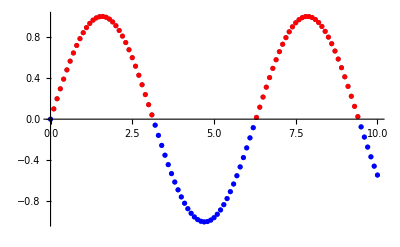

#### Solution

```mathematica
x=Table[x,{x,0,10,0.1}];
y=Sin[x];
data=MapThread[If[#2>0,Style[{#1,#2},Red],Style[{#1,#2},Blue]]&,{x,y}];
```

```mathematica
ListPlot[data]
```

-Graphics-

### Question Subsection

We have seen the HeavisideTheta in previous exercise notebooks. Recall that the Heaviside function is one that returns zero for negative inputs, and one for positive inputs. At x=0, we defined the value to be 1/2. Define your own Heaviside function, and plot it.

#### Solution

```mathematica
myHeaviside[x_]:=Which[x<0,0,x==0,1/2,x>0,1]
myHeaviside[x_List]:=myHeaviside/@x
```

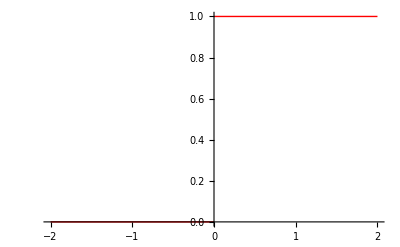

```mathematica
Plot[myHeaviside[x],{x,-2,2},PlotStyle->{Red,Thick}]
```